```mathematica
alpha =1
v = 1
n = 30
R = 2*Log[n/v]
f = alpha*((Sinh[alpha*#])/(Cosh[alpha*R] -1))&
```

1

1

30

2 Log[30]

(alpha Sinh[alpha #1])/(Cosh[alpha R]-1)&

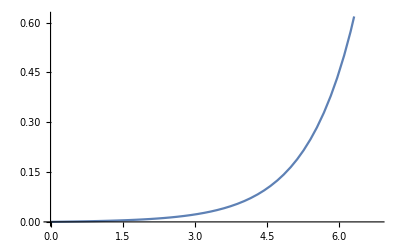

```mathematica
Plot[f[x], {x, 0, R}]
```